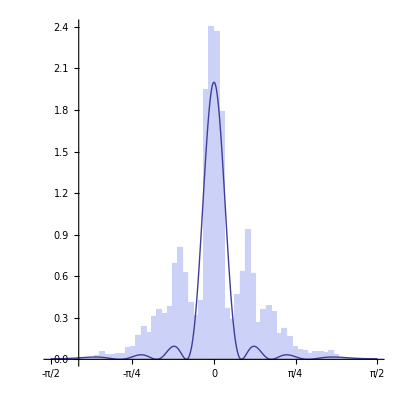
-Graphics-10

```mathematica
ReadDataSingle = Flatten[Import["HydroSingleSlitC120W12.dat"]];
Labeled[Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14},Ticks->{{-π/2,-π/4,0,π/4,π/2},Automatic}],Plot[{2.0(Sinc[12 Sin[x]]^2)},{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}],ToString[10],{{Right,Top}}]
```

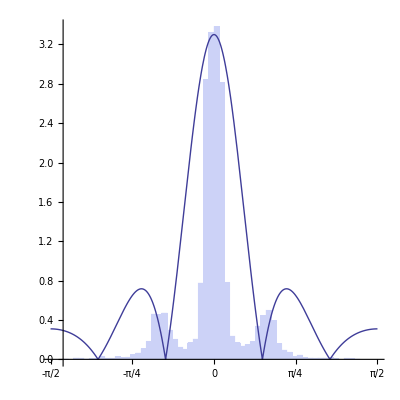
-Graphics-10

```mathematica
ReadDataSingle = Flatten[Import["HydroSingleSlitC160W7.dat"]];
Labeled[Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->30},Ticks->{{-π/2,-π/4,0,π/4,π/2},Automatic}],Plot[{3.3(Abs[Sinc[1.0π (14/(2π)) Sin[x]]])},{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}],ToString[10],{{Right,Top}}]
```

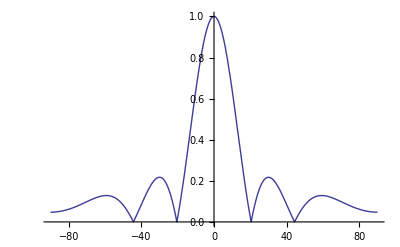

```mathematica
Plot[{(Abs[Sinc[1.0π 2.86 Sin[x 2π/360]]])},{x,-90,90},PlotRange->All]
```

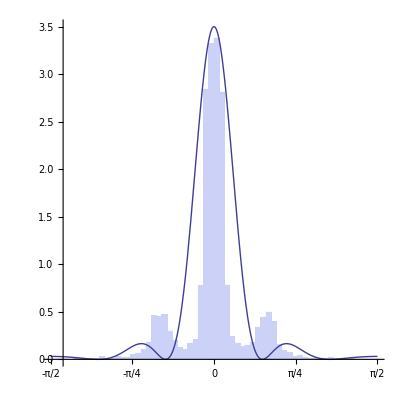
-Graphics-10

```mathematica
ReadDataSingle = Flatten[Import["HydroSingleSlitC160W7.dat"]];
Labeled[Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->30},Ticks->{{-π/2,-π/4,0,π/4,π/2},Automatic}],Plot[{3.5(Sinc[14/2 Sin[x]])^2},{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}],ToString[10],{{Right,Top}}]
```

```mathematica
yyyHank[x_,y_,t_,k_,w_]=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(18),{d,8,10,0.25}];
```

```mathematica
yyyHank[x_,y_,t_,k_,w_]
```

1/18 (BesselJ[0,k_ √(x_^2+(-8.+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(8.+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-8.+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(8.+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-8.25+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(8.25+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-8.25+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(8.25+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-8.5+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(8.5+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-8.5+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(8.5+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-8.75+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(8.75+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-8.75+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(8.75+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-9.+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(9.+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-9.+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(9.+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-9.25+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(9.25+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-9.25+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(9.25+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-9.5+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(9.5+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-9.5+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(9.5+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-9.75+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(9.75+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-9.75+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(9.75+y_)^2)] Sin[t_ w_])+1/18 (BesselJ[0,k_ √(x_^2+(-10.+y_)^2)] Cos[t_ w_]+BesselJ[0,k_ √(x_^2+(10.+y_)^2)] Cos[t_ w_]+BesselY[0,k_ √(x_^2+(-10.+y_)^2)] Sin[t_ w_]+BesselY[0,k_ √(x_^2+(10.+y_)^2)] Sin[t_ w_])

```mathematica
DaForceX[x_,y_,t_,k_,w_] = -D[yyyHank[x,y,t,k,w],x];
DaForceY[x_,y_,t_,k_,w_] = -D[yyyHank[x,y,t,k,w],y];
DaForceTanhX[x_,y_,t_,k_,w_] = -Tanh[D[yyyHankRand[x,y,t,k,w],x]];
DaForceTanhY[x_,y_,t_,k_,w_] = -Tanh[D[yyyHankRand[x,y,t,k,w],y]];
CosDisSqWidth = ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]
AngleDis[σ_] =ProbabilityDistribution[ⅇ^(-ϕ^2/σ^2) Cos[ϕ]^2,{ϕ,-π/2,π/2}]
SincSqWidth[d_] = ProbabilityDistribution[Sinc[x π/(d)]^2/d,{x,-π/2,π/2}]
```

ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]

ProbabilityDistribution[ⅇ^(-x^2/σ^2) Cos[x]^2,{x,-π/2,π/2}]

ProbabilityDistribution[Sinc[(x π)/d]^2/d,{x,-π/2,π/2}]

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 120;
swidth = 1;
CHUNK = 8*16;
REPEAT = 1000;
CUTTOFF = 80;
phase = -1/2.0;
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
MEMORYLIST = {10,15,30,40};

Do[
Close["HydroDoubleSlitAutoC80M"<> ToString[MEMVALUE]<>".dat"]
,{MEMVALUE,MEMORYLIST}]

Do[
Do[
outstream=OpenAppend["HydroDoubleSlitAutoC80M"<> ToString[MEMVALUE]<>".dat"];

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMVALUE)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMVALUE)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMVALUE)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMVALUE)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=40,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=40,ttt < tmax, ttt+=0.1, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]
,{MEMVALUE,MEMORYLIST}];
(*Close[outstream]*)
,{REPEAT}];
```

General::openx: "HydroDoubleSlitAutoC80M15.dat" is not open.

General::openx: "HydroDoubleSlitAutoC80M30.dat" is not open.

General::openx: "HydroDoubleSlitAutoC80M40.dat" is not open.

General::stop: Further output of General :: openx will be suppressed during this calculation.

$Aborted

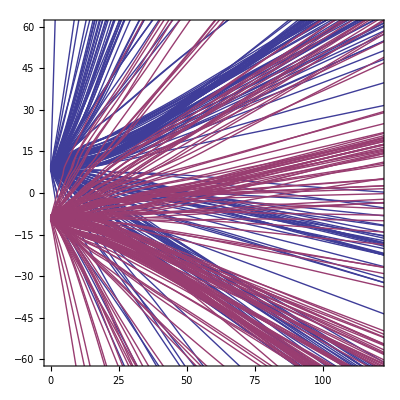

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 250;
xmax = 120;
NMAX=10*16;
swidth = 1;
phase = -π 1.3;
MEMORY = 40;

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMORY)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMORY)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{NMAX}];
];

ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
EmitSound[Play[Sin[1000 (1-t)^2],{t,0,1}]];
```

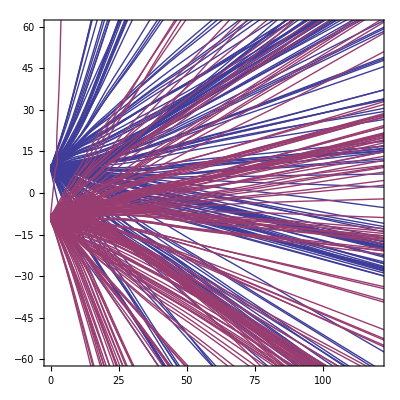

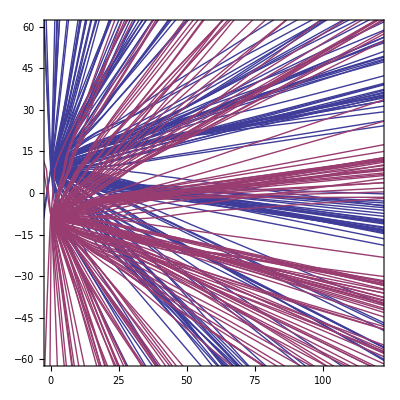

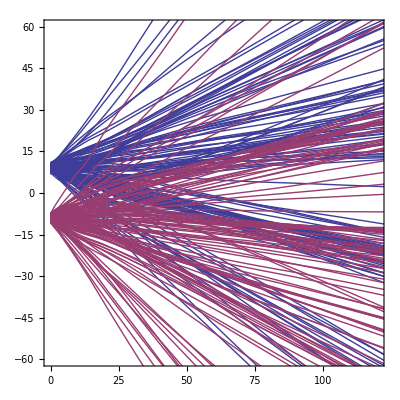

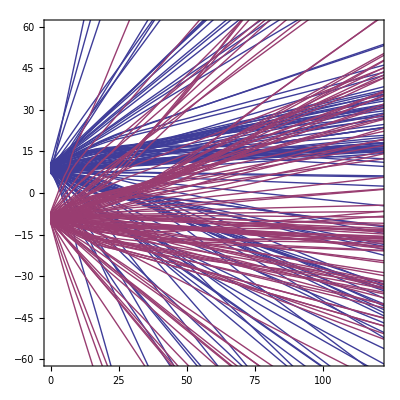

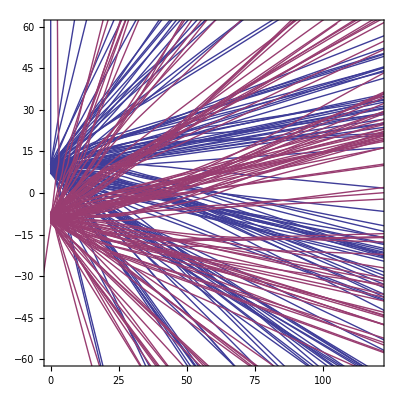

```mathematica
AAA =  1.0;
ddd = 9.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 100;
swidth = 2;
CHUNK = 100;
REPEAT = 1000;
CUTTOFF = 60;
phase = -π 1.3;
MEMORYLIST = {1,2.5,5,7.5,10,12.5,15,20,30,40};
MEMORYLIST = {10,15,40};

Do[
Close["HydroDoubleSlitAutoC60M"<> ToString[MEMVALUE]<>".dat"]
,{MEMVALUE,MEMORYLIST}]

Do[
Do[
outstream=OpenAppend["HydroDoubleSlitAutoC60M"<> ToString[MEMVALUE]<>".dat"];

Parallelize[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] == ⅇ^(-t/MEMVALUE)( AAA DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] ==ⅇ^(-t/MEMVALUE)( AAA DaForceY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]],x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMVALUE)(AAA  DaForceX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMVALUE)(AAA  DaForceY[x[t],y[t],t+phase,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==Sin[RandomVariate[CosDisSqWidth]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}];
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=20,ttt < tmax, ttt+=0.1, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]

(*Beep[]*)
EmitSound[Play[Sin[2000 t^2],{t,0,1}]];

,{MEMVALUE,MEMORYLIST}];
(*Close[outstream]*)
,{REPEAT}];
```

General::openx: "HydroDoubleSlitAutoC60M10.dat" is not open.

General::openx: "HydroDoubleSlitAutoC60M15.dat" is not open.

General::openx: "HydroDoubleSlitAutoC60M40.dat" is not open.

General::stop: Further output of General :: openx will be suppressed during this calculation.

$Aborted